```mathematica
data=Import["C:/Users/gospodan/Downloads/wignerfunction.xlsx"];
```

```mathematica
data=First[data];
data=Rest[data];
```

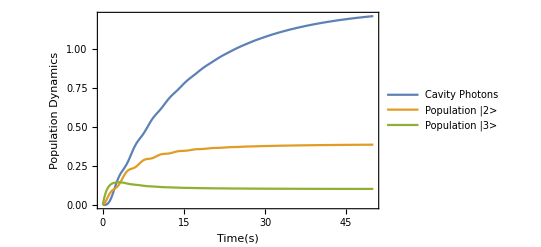

```mathematica
ListLinePlot[{data[[All,{1,2}]],data[[All,{1,3}]],data[[All,{1,4}]]},Frame->True,FrameLabel->{"Time(s)","Population Dynamics"},PlotLegends->{"Cavity Photons","Population |2>","Population |3>"}]
```

```mathematica
pDyn=Legended[ListLinePlot[{data[[All,{1,2}]],data[[All,{1,3}]],data[[All,{1,4}]]},PlotStyle->{Directive[CapForm["Round"],Dashing[{0.014,0.014}],Red,Thickness[0.01]],Directive[Blue,Thickness[0.006]],Directive[Black,Thickness[0.008]]},Frame->True,FrameLabel->{"Time (s)","Population Dynamics"},FrameStyle->Directive[Black,AbsoluteThickness[1.25]],BaseStyle->{FontWeight->"Bold",FontSize->20},ImageSize->{600,500},PlotRange->All, PlotLabel->Style["",FontSize->25,Black]],Placed[Framed[LineLegend[{Directive[CapForm["Round"],Dashing[{0.014,0.014}],Red,Thickness[0.01]],Directive[Blue,Thickness[0.006]],Directive[Black,Thickness[0.006]]},{Style["Cavity Photons",Bold,12],Style["Population |2>",Bold,12],Style["Population |3>",Bold,12]},LegendLayout->"Column",LabelStyle->Directive[Bold,12]],Background->White,FrameStyle->Directive[Black,AbsoluteThickness[0.5]],RoundingRadius->0],Scaled[{0.2,0.82}]]
];
```

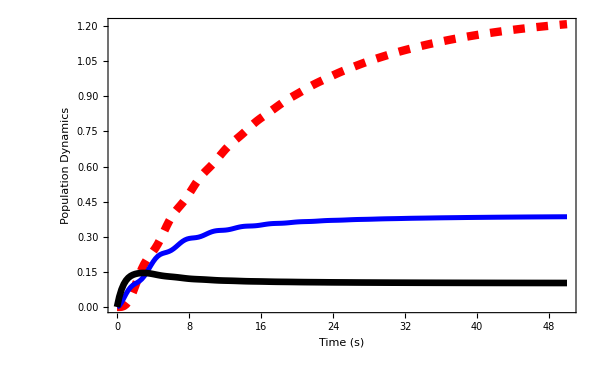

```mathematica
pDyn
```

```mathematica
pDyn2=ListLinePlot[{data[[All,{1,2}]],data[[All,{1,3}]],data[[All,{1,4}]]},PlotStyle->{Directive[CapForm["Round"],Dashing[{0.014,0.014}],Red,Thickness[0.01]],Directive[Blue,Thickness[0.006]],Directive[Black,Thickness[0.008]]},Frame->True,FrameTicks->{{Range[0,0.5,0.1],None}, {Automatic,Automatic}},FrameLabel->{""},FrameStyle->Directive[Black,AbsoluteThickness[1.25]],BaseStyle->{FontWeight->"Bold",FontSize->20},ImageSize->{600,500},PlotRange->{{0,6},{0,0.5}}, PlotLabel->Style["",FontSize->25,Black]];
```

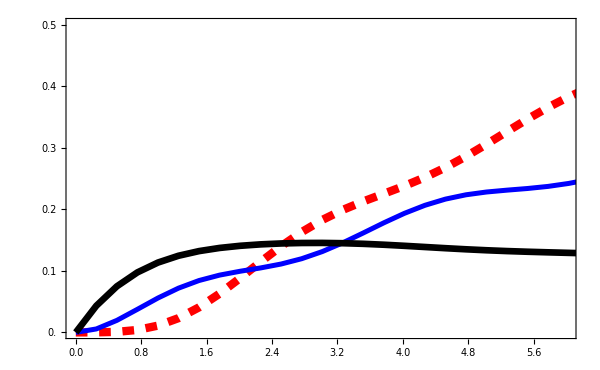

```mathematica
pDyn2
```

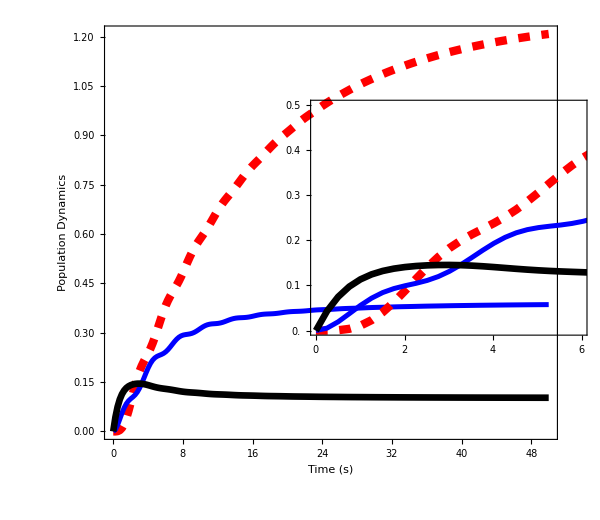

```mathematica
Show[Graphics[{Rectangle[{-2,1},{13,10},pDyn],Rectangle[{5.1,3.8},{13.5,8.5},pDyn2]}],ImageSize->{600,520}]
```

```mathematica
pDyn3=Legended[ListLinePlot[{data[[All,{1,2}]],data[[All,{1,3}]],data[[All,{1,4}]]},PlotStyle->{Directive[CapForm["Round"],Dashing[{0.014,0.014}],Red,Thickness[0.01]],Directive[Blue,Thickness[0.006]],Directive[Black,Thickness[0.008]]},Frame->True,FrameLabel->{"Time (s)",""},FrameStyle->Directive[Black,AbsoluteThickness[1.25]],BaseStyle->{FontWeight->"Bold",FontSize->20},ImageSize->{600,500},PlotRange->All,PlotLabel->Style["Population Dynamics",FontSize->20,Black,Bold],
 PlotLabel->Style["",FontSize->25,Black]],Placed[Framed[LineLegend[{Directive[CapForm["Round"],Dashing[{0.014,0.014}],Red,Thickness[0.01]],Directive[Blue,Thickness[0.006]],Directive[Black,Thickness[0.006]]},{Style["Cavity Photons",Bold,12],Style["Population |2⟩",Bold,12],Style["Population |3⟩",Bold,12]},LegendLayout->"Column",LabelStyle->Directive[Bold,12]],Background->White,FrameStyle->Directive[Black,AbsoluteThickness[0.5]],RoundingRadius->0],Scaled[{0.7,0.57}]]
];
```

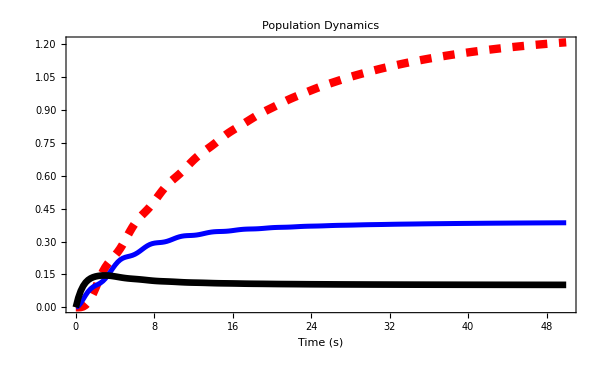

```mathematica
pDyn3
```

```mathematica
pDyn4 = Show[Graphics[{Rectangle[{-2,1},{13,10},pDyn3]}],ImageSize->{600,520}]
```

-Graphics-

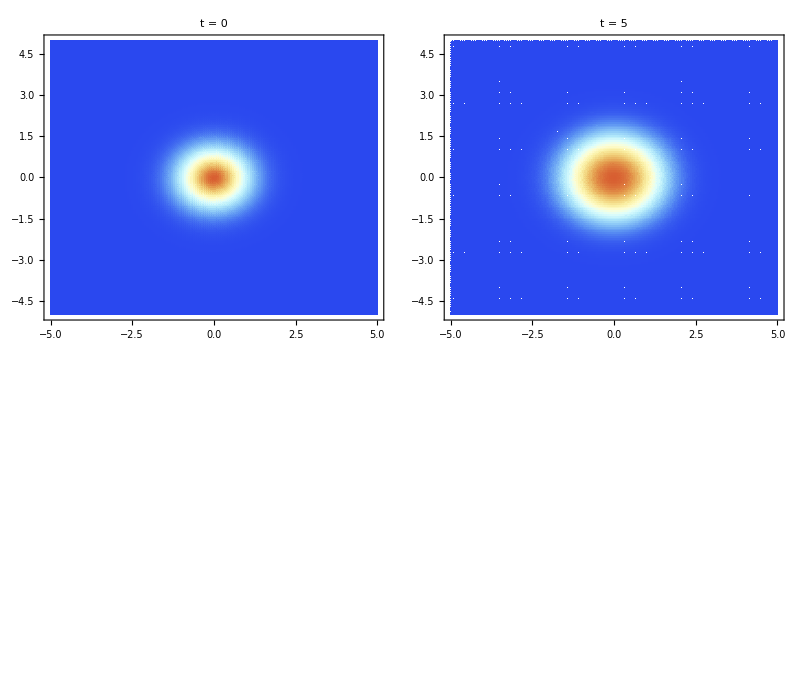

```mathematica
file="C:/Users/gospodan/Downloads/wignerphasespace.xlsx";
sheets=Import[file,"Sheets"];

makeWignerPlot[sheet_]:=Module[{wraw,xvals,yvals,W},wraw=Import[file,{"Data",sheet}];
xvals=N@Rest[wraw[[1]]];
yvals=N@Rest[wraw[[All,1]]];
W=N@(Rest/@Rest[wraw]);
ListDensityPlot[W,DataRange->{{Min[xvals],Max[xvals]},{Min[yvals],Max[yvals]}},Frame->True,FrameLabel->{""},FrameStyle->Directive[Black,AbsoluteThickness[0.8]],BaseStyle->{FontWeight->"Bold",FontSize->18},PlotRange->All,ColorFunction->"LightTemperatureMap",ImageSize->{400,350},PlotLabel->Style[StringReplace[sheet,"Wigner_t"->"t = "],Bold,14,Black]]]

plots=makeWignerPlot/@sheets;

GraphicsGrid[Partition[plots,UpTo[2]],Spacings->{0.5,0.5}]
```

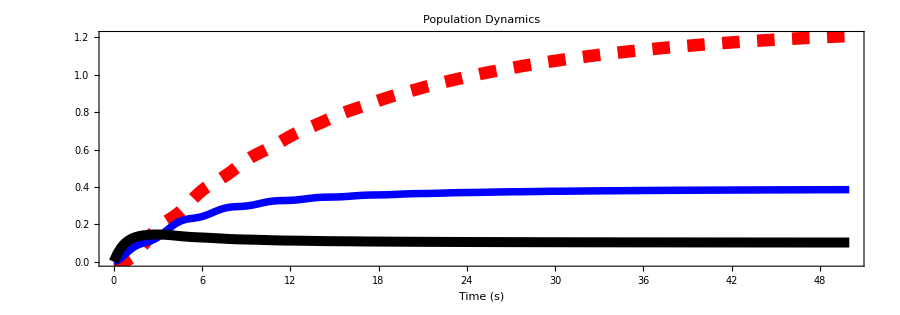

```mathematica
pDyn5=Show[pDyn3,ImageSize->900,PlotRange->All,AspectRatio->0.35,ImagePadding->{{62,32},{25,10}}]
```

```mathematica
bottomPlots=Show[#,ImageSize->200,ImagePadding->{{35,10},{30,10}},AspectRatio->1]&/@plots;

finalFig=Grid[{{Item[pDyn5,Alignment->Center]},{GraphicsRow[bottomPlots,Spacings->15,ImageSize->900]}},Spacings->{0,1},Alignment->Center];

finalFig
```

-Graphics-

```mathematica
Export["C:/Users/gospodan/Downloads/wigner plot.jpg",finalFig]
```

C:/Users/gospodan/Downloads/wigner plot.jpg